```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Oc={0,0,0,1};
Oc2={6,0,0,1};
zeta1 = -2;
zeta2=-1;
alpha=45;
beta = 0;
Oc2={6,0,0,1};
Rot1=RotationsE2[alpha];
Rot2=RotationsE2[beta];
```

M =(1/(√2) | 0 | -1/(√2) | -3 √2
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | -3 √2
0 | 0 | 0 | 1)

ProjectionMtxCamera1(-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(-1/(√2) | 0 | 1/(√2) | 3 √2
0 | -1 | 0 | 0
-1/(√2) | 0 | -1/(√2) | 3 √2
1/(√2) | 0 | 1/(√2) | -3 √2)

CameraProjectedPointsK1 = (-6 | -6 | 8 | -4
-10 | -6 | 8 | -4
-10 | -10 | 8 | -4
-6 | -10 | 8 | -4
-6 | -6 | 12 | -6
-10 | -6 | 12 | -6
-10 | -10 | 12 | -6
-6 | -10 | 12 | -6
-16 | -16 | 12 | -6)

CameraProjectedPointsK2 = (-1/(√2) | -3 | 7/(√2) | -7/(√2)
-3/(√2) | -3 | 5/(√2) | -5/(√2)
-3/(√2) | -5 | 5/(√2) | -5/(√2)
-1/(√2) | -5 | 7/(√2) | -7/(√2)
-3/(√2) | -3 | 9/(√2) | -9/(√2)
-5/(√2) | -3 | 7/(√2) | -7/(√2)
-5/(√2) | -5 | 7/(√2) | -7/(√2)
-3/(√2) | -5 | 9/(√2) | -9/(√2)
-4 √2 | -8 | 2 √2 | -2 √2)

homogene CameraProjectedPointsK1 = (3/2 | 3/2 | -2 | 1
5/2 | 3/2 | -2 | 1
5/2 | 5/2 | -2 | 1
3/2 | 5/2 | -2 | 1
1 | 1 | -2 | 1
5/3 | 1 | -2 | 1
5/3 | 5/3 | -2 | 1
1 | 5/3 | -2 | 1
8/3 | 8/3 | -2 | 1)

homogene CameraProjectedPointsK2 = (1/7 | (3 √2)/7 | -1 | 1
3/5 | (3 √2)/5 | -1 | 1
3/5 | √2 | -1 | 1
1/7 | (5 √2)/7 | -1 | 1
1/3 | (√2)/3 | -1 | 1
5/7 | (3 √2)/7 | -1 | 1
5/7 | (5 √2)/7 | -1 | 1
1/3 | (5 √2)/9 | -1 | 1
2 | 2 √2 | -1 | 1)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

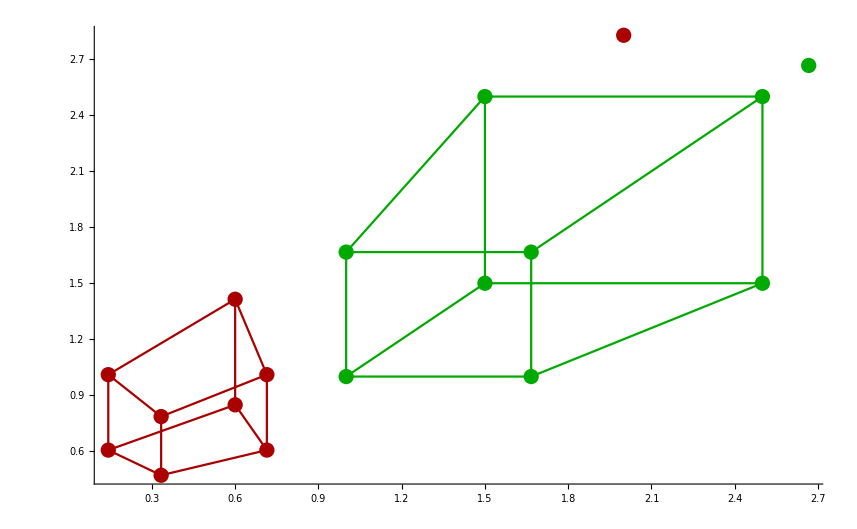

ImagePlaneC1Points = (3/2 | 3/2 | 1
5/2 | 3/2 | 1
5/2 | 5/2 | 1
3/2 | 5/2 | 1
1 | 1 | 1
5/3 | 1 | 1
5/3 | 5/3 | 1
1 | 5/3 | 1
8/3 | 8/3 | 1)

ImagePlaneC2Points = (1/7 | (3 √2)/7 | 1
3/5 | (3 √2)/5 | 1
3/5 | √2 | 1
1/7 | (5 √2)/7 | 1
1/3 | (√2)/3 | 1
5/7 | (3 √2)/7 | 1
5/7 | (5 √2)/7 | 1
1/3 | (5 √2)/9 | 1
2 | 2 √2 | 1)

CoefficientMtx = (3/14 | 3/14 | 1/7 | 9/(7 √2) | 9/(7 √2) | (3 √2)/7 | 3/2 | 3/2 | 1
3/2 | 9/10 | 3/5 | 3/(√2) | 9/(5 √2) | (3 √2)/5 | 5/2 | 3/2 | 1
3/2 | 3/2 | 3/5 | 5/(√2) | 5/(√2) | √2 | 5/2 | 5/2 | 1
3/14 | 5/14 | 1/7 | 15/(7 √2) | 25/(7 √2) | (5 √2)/7 | 3/2 | 5/2 | 1
1/3 | 1/3 | 1/3 | (√2)/3 | (√2)/3 | (√2)/3 | 1 | 1 | 1
25/21 | 5/7 | 5/7 | (5 √2)/7 | (3 √2)/7 | (3 √2)/7 | 5/3 | 1 | 1
25/21 | 25/21 | 5/7 | (25 √2)/21 | (25 √2)/21 | (5 √2)/7 | 5/3 | 5/3 | 1
1/3 | 5/9 | 1/3 | (5 √2)/9 | (25 √2)/27 | (5 √2)/9 | 1 | 5/3 | 1
16/3 | 16/3 | 2 | (16 √2)/3 | (16 √2)/3 | 2 √2 | 8/3 | 8/3 | 1)

RowReduce CoefficientMtx = [(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)]

ns ={{0,1,0,0,0,-2 √2,0,1,0}}

F = (0 | 1 | 0
0 | 0 | -2 √2
0 | 1 | 0)

lC1 = {{3/2,-2 √2,3/2},{3/2,-2 √2,3/2},{5/2,-2 √2,5/2},{5/2,-2 √2,5/2},{1,-2 √2,1},{1,-2 √2,1},{5/3,-2 √2,5/3},{5/3,-2 √2,5/3},{8/3,-2 √2,8/3}}

lPrimeC1 = {{0,8/7,-12/7},{0,8/5,-12/5},{0,8/5,-4},{0,8/7,-20/7},{0,4/3,-4/3},{0,12/7,-12/7},{0,12/7,-20/7},{0,4/3,-20/9},{0,3,-8}}

e = {1,0,0}

e' = {-1,0,1}

EpipoleLines = (1 | -(4 √2)/3 | 1
1 | -(4 √2)/3 | 1
1 | -(4 √2)/5 | 1
1 | -(4 √2)/5 | 1
1 | -2 √2 | 1
1 | -2 √2 | 1
1 | -(6 √2)/5 | 1
1 | -(6 √2)/5 | 1
1 | -3/(2 √2) | 1)

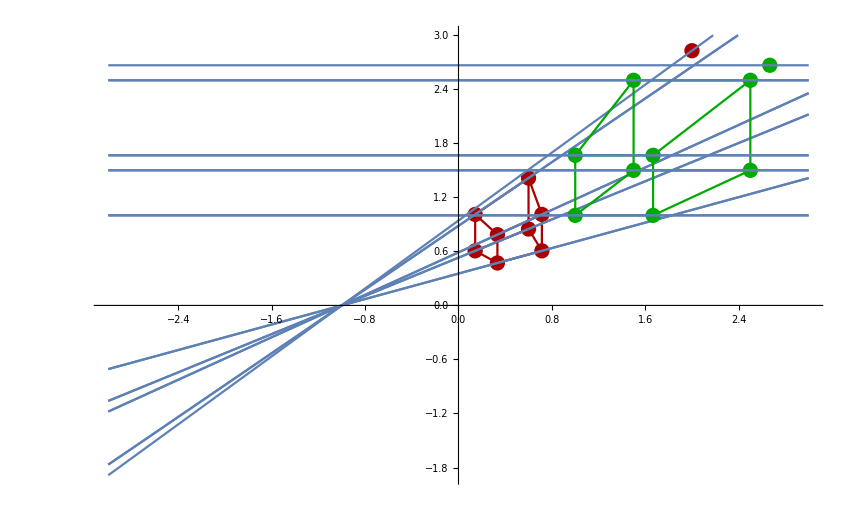

EMtx = {{0,1/(√2),0},{0,0,1},{0,-1/(√2),0}}

U of E = {{0,1/(√2),1/(√2)},{1,0,0},{0,-1/(√2),1/(√2)}}

Sigma of E = {{1,0,0},{0,1,0},{0,0,0}}

V of E = {{0,0,1},{0,1,0},{1,0,0}}

S1 = (0 | 1/(√2) | 0
-1/(√2) | 0 | 1/(√2)
0 | -1/(√2) | 0)

S2 = (0 | -1/(√2) | 0
1/(√2) | 0 | -1/(√2)
0 | 1/(√2) | 0)

R1 = (1/(√2) | 0 | -1/(√2)
0 | 1 | 0
1/(√2) | 0 | 1/(√2))

R2 = (1/(√2) | 0 | 1/(√2)
0 | -1 | 0
1/(√2) | 0 | -1/(√2))

{{1/(√2),0,-1/(√2)},{0,1,0},{1/(√2),0,1/(√2)}} is Rotation

{{1/(√2),0,1/(√2)},{0,-1,0},{1/(√2),0,-1/(√2)}} is Rotation

Check if t of S1, S2 is equal = {{{1,0,1}},{{1,0,1}}}

t = {1,0,1}

P21  = (1/(√2) | 0 | 1/(√2) | -1
0 | -1 | 0 | 0
1/(√2) | 0 | -1/(√2) | -1)

P22  = (1/(√2) | 0 | -1/(√2) | -1
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | -1)

P23  = (1/(√2) | 0 | 1/(√2) | 1
0 | -1 | 0 | 0
1/(√2) | 0 | -1/(√2) | 1)

P24  = (1/(√2) | 0 | -1/(√2) | 1
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | 1)

Triangulation: WorldPoint reconstruction ___________________________________________________

C2Oc2 = {-1,0,-1}

WOc2 = {√2,0,0}

ImagePlanePoints2 =((4 √2)/7 | (3 √2)/7 | -(4 √2)/7 | 1
(4 √2)/5 | (3 √2)/5 | -(4 √2)/5 | 1
(4 √2)/5 | √2 | -(4 √2)/5 | 1
(4 √2)/7 | (5 √2)/7 | -(4 √2)/7 | 1
(2 √2)/3 | (√2)/3 | -(2 √2)/3 | 1
(6 √2)/7 | (3 √2)/7 | -(6 √2)/7 | 1
(6 √2)/7 | (5 √2)/7 | -(6 √2)/7 | 1
(2 √2)/3 | (5 √2)/9 | -(2 √2)/3 | 1
3/(√2) | 2 √2 | -3/(√2) | 1)

ImagePlanePoints1 =(3/2 | 3/2 | -2 | 1
5/2 | 3/2 | -2 | 1
5/2 | 5/2 | -2 | 1
3/2 | 5/2 | -2 | 1
1 | 1 | -2 | 1
5/3 | 1 | -2 | 1
5/3 | 5/3 | -2 | 1
1 | 5/3 | -2 | 1
8/3 | 8/3 | -2 | 1)

LinesC1 = {{3/2+(3 t)/2,3/2+(3 t)/2,-2-2 t},{5/2+(5 t)/2,3/2+(3 t)/2,-2-2 t},{5/2+(5 t)/2,5/2+(5 t)/2,-2-2 t},{3/2+(3 t)/2,5/2+(5 t)/2,-2-2 t},{1+t,1+t,-2-2 t},{5/3+(5 t)/3,1+t,-2-2 t},{5/3+(5 t)/3,5/3+(5 t)/3,-2-2 t},{1+t,5/3+(5 t)/3,-2-2 t},{8/3+(8 t)/3,8/3+(8 t)/3,-2-2 t}}

LinesC2 = {{1/7 √2 (4-3 t2),3/7 √2 (1+t2),-4/7 √2 (1+t2)},{-1/5 √2 (-4+t2),3/5 √2 (1+t2),-4/5 √2 (1+t2)},{-1/5 √2 (-4+t2),√2 (1+t2),-4/5 √2 (1+t2)},{1/7 √2 (4-3 t2),5/7 √2 (1+t2),-4/7 √2 (1+t2)},{-1/3 √2 (-2+t2),1/3 √2 (1+t2),-2/3 √2 (1+t2)},{-1/7 √2 (-6+t2),3/7 √2 (1+t2),-6/7 √2 (1+t2)},{-1/7 √2 (-6+t2),5/7 √2 (1+t2),-6/7 √2 (1+t2)},{-1/3 √2 (-2+t2),5/9 √2 (1+t2),-2/3 √2 (1+t2)},{(3+t2)/(√2),2 √2 (1+t2),-(3 (1+t2))/(√2)}}

t & t2 = {t→1/3 (-3+√2),t2→1/6,t→1/3 (-3+√2),t2→-1/6,t→1/3 (-3+√2),t2→-1/6,t→1/3 (-3+√2),t2→1/6,t→-1+1/(√2),t2→1/2,t→-1+1/(√2),t2→1/6,t→-1+1/(√2),t2→1/6,t→-1+1/(√2),t2→1/2,t→-1+1/(√2),t2→-1/3}

ReconstructedPointsC1 = {{{{0.707107},{0.707107},{-0.942809}}},{{{1.17851},{0.707107},{-0.942809}}},{{{1.17851},{1.17851},{-0.942809}}},{{{0.707107},{1.17851},{-0.942809}}},{{{0.707107},{0.707107},{-1.41421}}},{{{1.17851},{0.707107},{-1.41421}}},{{{1.17851},{1.17851},{-1.41421}}},{{{0.707107},{1.17851},{-1.41421}}}}

ReconstructedPointsC2 = {{{{0.707107},{0.707107},{-0.942809}}},{{{1.17851},{0.707107},{-0.942809}}},{{{1.17851},{1.17851},{-0.942809}}},{{{0.707107},{1.17851},{-0.942809}}},{{{0.707107},{0.707107},{-1.41421}}},{{{1.17851},{0.707107},{-1.41421}}},{{{1.17851},{1.17851},{-1.41421}}},{{{0.707107},{1.17851},{-1.41421}}}}

```mathematica
StartComputation[];
```